```mathematica
GetPlotRange::usage="GetPlotRange[gr] returns the actual unpadded plot range of graphics gr. GetPlotRange[gr, True] returns the actual padded plot range of gr. GetPlotRange can handle Graphics, Graphics3D and Graph objects.";
GetPlotRange[_[gr:(_Graphics|_Graphics3D|_Graph|_GeoGraphics),___],pad_]:=GetPlotRange[gr,pad];(*Handle Legended[…] and similar.*)GetPlotRange[gr_GeoGraphics,False]:=(PlotRange/.Quiet@AbsoluteOptions@gr);(*TODO:does not handle PlotRangePadding.*)GetPlotRange[gr_Graph,pad_: False]:=Charting`get2DPlotRange[gr,pad];
GetPlotRange[gr:(_Graphics|_Graphics3D),pad_: False]:=Module[{r=PlotRange/.Options@gr},If[MatrixQ[r,NumericQ],(*TODO:does not handle PlotRangePadding*)r,Last@Last@Reap@Rasterize[Show[gr,If[pad===False,PlotRangePadding->None,{}],Axes->True,Frame->False,Ticks->((Sow@{##};Automatic)&),DisplayFunction->Identity,ImageSize->0],ImageResolution->1]]];


(*Joins and filters options,keeping the righmost if there are multiple instances of the same option.*)
filter[opts_List,head_]:=Reverse@DeleteDuplicatesBy[Reverse@FilterRules[Flatten@opts,First/@Options@head],First];


(*Find and use SETools of Szabolcs& Halirutan*)
$SEToolsExist=FileExistsQ@FileNameJoin@{$UserBaseDirectory,"Applications","SETools","Java","SETools.jar"};

(*If SETools exist,initiate JLink and include some functions*)
If[$SEToolsExist,Needs@"JLink`";
JLink`InstallJava[];
copyToClipboard[text_]:=Module[{nb},nb=NotebookCreate[Visible->False];
NotebookWrite[nb,Cell[text,"Input"]];
SelectionMove[nb,All,Notebook];
FrontEndTokenExecute[nb,"Copy"];
NotebookClose@nb;];
uploadButtonAction[img_]:=uploadButtonAction[img,"![Mathematica graphics](",")"];
uploadButtonAction[img_,wrapStart_String,wrapEnd_String]:=Module[{url},Check[url=stackImage@img,Return[]];
copyToClipboard@(wrapStart<>url<>wrapEnd);];
stackImage::httperr="Server returned respose code: `1`";
stackImage::err="Server returner error: `1`";
stackImage::parseErr="Could not parse the answer of the server.";
stackImage[g_]:=Module[{url,client,method,data,partSource,part,entity,code,response,error,result,parseXMLOutput},parseXMLOutput[str_String]:=Block[{xml=ImportString[str,{"HTML","XMLObject"}],result},result=Cases[xml,XMLElement["script",_,res_]:>StringTrim[res],Infinity]/.{{s_String}}:>s;
If[result=!={}&&StringMatchQ[result,"window.parent"~~__],Flatten@StringCases[result,"window.parent."~~func__~~"("~~arg__~~");":>{StringMatchQ[func,"closeDialog"],StringTrim[arg,"\""]}],$Failed]];
parseXMLOutput[___]:=$Failed;
data=ExportString[g,"PNG"];
JLink`JavaBlock[JLink`LoadJavaClass["de.halirutan.se.tools.SEUploader",StaticsVisible->True];
response=Check[SEUploader`sendImage@ToCharacterCode@data,Return@$Failed]];
If[response===$Failed,Return@$Failed];
result=parseXMLOutput@response;
If[result=!=$Failed,If[TrueQ@First@result,Last@result,Message[stackImage::err,Last@result];$Failed],Message[stackImage::parseErr];$Failed]];];


GraphicsButton::usage="GraphicsButton[lbl, gr] represent a button that is labeled with lbl and offers functionality for the static graphics object gr. GraphicsButton[gr] uses a tiny version of gr as label.";
MenuItems::usage="MenuItems is an option for GraphicsButton that specifies additional label :> command pairs as a list to be included at the top of the action menu of GraphicsButton.";
Options[GraphicsButton]=DeleteDuplicatesBy[Flatten@{MenuItems->{},RasterSize->Automatic,ColorSpace->Automatic,ImageResolution->300,Options@ActionMenu},First];
GraphicsButton[expr_,opts:OptionsPattern[]]:=GraphicsButton[Pane[expr,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],expr,opts];
GraphicsButton[lbl_,expr_,opts:OptionsPattern[]]:=Module[{head,save,items=OptionValue@MenuItems,rasterizeOpts,dir=$UserDocumentsDirectory,file=""},rasterizeOpts=filter[{Options@GraphicsButton,opts},Options@Rasterize];
save[format_]:=(file=SystemDialogInput["FileSave",FileNameJoin@{dir,"."<>ToLowerCase@format}];
If[file=!=$Failed&&file=!=$Canceled,dir=DirectoryName@file;
Quiet@Export[file,If[format==="NB",expr,Rasterize[expr,"Image",rasterizeOpts]],format]]);
head=Head@Unevaluated@expr;
ActionMenu[lbl,Flatten@{If[items=!={},items,Nothing],"Copy expression":>CopyToClipboard@expr,"Copy image":>CopyToClipboard@Rasterize@expr,"Copy high-res image":>CopyToClipboard@Rasterize[expr,"Image",rasterizeOpts],"Paste expression":>Paste@expr,"Paste image":>Paste@Rasterize@expr,"Paste high-res image":>Paste@Rasterize[expr,"Image",rasterizeOpts],Delimiter,"Save as notebook…":>save@"NB","Save as JPEG…":>save@"JPEG","Save as TIFF…":>save@"TIFF","Save as BMP…":>save@"BMP",Delimiter,Style["Upload image to StackExchange",If[$SEToolsExist,Black,Gray]]:>If[$SEToolsExist,uploadButtonAction@Rasterize@expr],"Open image in external application":>Module[{f=Export[FileNameJoin@{$TemporaryDirectory,"temp_img.tiff"},Rasterize@expr,"TIFF"]},If[StringQ@f&&FileExistsQ@f,SystemOpen@f]]},filter[{Options@GraphicsButton,opts,{Method->"Queued"}},Options@ActionMenu]]];


PlotExplorer::usage="PlotExplorer[plot] returns a manipulable version of plot. PlotExplorer can handle Graph and Graphics objects and plotting functions like Plot, LogPlot, ListPlot, DensityPlot, Streamplot, etc. PlotExplorer allows the modification of the plot range, image size and aspect ratio. If the supplied argument is a full specification of a plotting function holding its first argument (e.g. Plot) the result offers functionality to replot the function to the modified plot range. PlotExplorer has attribute HoldFirst.";
AppearanceFunction::usage="AppearanceFunction is an option for PlotExplorer that specifies the appearance function of the menu button. Use Automatic for the default appearance, Identity to display a classic button or None to omit the menu button.";
MenuPosition::usage="MenuPosition is an option for PlotExplorer that specifies the position of the (upper right corner of the) menu button within the graphics object.";
Attributes[PlotExplorer]={HoldFirst};
Options[PlotExplorer]={AppearanceFunction->(Mouseover[Invisible@#,#]&@Framed[#,Background->GrayLevel[.5,.5],RoundingRadius->5,FrameStyle->None,Alignment->{Center,Center},BaseStyle->{FontFamily->"Helvetica"}]&),MenuPosition->Scaled@{1,1}};
PlotExplorer[expr_,rangeArg_: Automatic,sizeArg_: Automatic,ratioArg_: Automatic,opts:OptionsPattern[]]:=Module[{plot=expr,held=Hold@expr,head,holdQ=True,legQ=False,appearance,position,$1Dplots=Plot|LogPlot|LogLinearPlot|LogLogPlot,$2Dplots=DensityPlot|ContourPlot|RegionPlot|StreamPlot|StreamDensityPlot|VectorPlot|VectorDensityPlot|LineIntegralConvolutionPlot|GeoGraphics},head=held[[1,0]];
If[head===Symbol,holdQ=False;head=Head@expr];
If[head===Legended,legQ=True;
If[holdQ,held=held/.Legended[x_,___]:>x;
head=held[[1,0]],head=Head@First@expr]];
holdQ=holdQ&&MatchQ[head,$1Dplots|$2Dplots];
If[!holdQ,legQ=Head@expr===Legended;
head=If[legQ,Head@First@expr,Head@expr]];
If[Not@MatchQ[head,$1Dplots|$2Dplots|Graphics|Graph],expr,DynamicModule[{dyn,gr,leg,replot,rescale,new,mid,len,min=0.1,f={1,1},set,d,epilog,over=False,defRange,range,size,ratio,pt1,pt1sc=None,pt2=None,pt2sc=None,rect,button},{gr,leg}=If[legQ,List@@plot,{plot,None}];
size=If[sizeArg===Automatic,Rasterize[gr,"RasterSize"],Setting@sizeArg];
defRange=If[rangeArg===Automatic,GetPlotRange[gr,False],Setting@rangeArg];
ratio=If[ratioArg===Automatic,Divide@@Reverse@size,Setting@ratioArg];
epilog=Epilog/.Quiet@AbsoluteOptions@plot;
gr=plot;
(*When r1 or r2 is e.g.{1,1} (scale region has zero width),EuclideanDistance by defult returns Infinity which is fine.*)d[p1_,p2_,{r1_,r2_}]:=Quiet@N@EuclideanDistance[Rescale[p1,r1],Rescale[p2,r2]];
set[r_]:=(range=new=r;mid=Mean/@range;
len=Abs[Subtract@@@range];pt1=None;rect={};);
set@defRange;
(*Replace plot range or insert if nonexistent*)replot[h_,hold_,r_]:=Module[{temp},ReleaseHold@Switch[h,$1Dplots,temp=ReplacePart[hold,{{1,2,2}->r[[1,1]],{1,2,3}->r[[1,2]]}];
If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->r)},Insert[temp,PlotRange->r,{1,-1}]],$2Dplots,temp=ReplacePart[hold,{{1,2,2}->r[[1,1]],{1,2,3}->r[[1,2]],{1,3,2}->r[[2,1]],{1,3,3}->r[[2,2]]}];
If[MemberQ[temp,PlotRange,Infinity],temp/.{_[PlotRange,_]->(PlotRange->r)},Insert[temp,PlotRange->r,{1,-1}]],_,hold]];
rescale[h_,hold_,sc_]:=ReleaseHold@Switch[h,$1Dplots|$2Dplots,If[MemberQ[hold,ScalingFunctions,Infinity],hold/.{_[ScalingFunctions,_]->(ScalingFunctions->sc)},Insert[hold,ScalingFunctions->sc,{1,-1}]],_,hold];
appearance=OptionValue@AppearanceFunction/.{Automatic:>(AppearanceFunction/.Options@PlotExplorer)};
position=OptionValue@MenuPosition/.Automatic->Scaled@{1,1};
(*Print@Column@{rangeArg,sizeArg,ratioArg,appearance,position};*)button=If[appearance===None,{},Inset[appearance@Dynamic@GraphicsButton["Menu",dyn,Appearance->If[appearance===Identity,Automatic,None],MenuItems->Flatten@{{Row@{"Copy PlotRange → ",TextForm/@range}:>(CopyToClipboard[PlotRange->range]),Row@{"Copy ImageSize → ",InputForm@size}:>(CopyToClipboard[ImageSize->size]),Row@{"Copy AspectRatio → ",InputForm@ratio}:>(CopyToClipboard[AspectRatio->ratio])},If[MatchQ[head,$1Dplots|$2Dplots],{Delimiter,"Replot at current PlotRange":>(gr=replot[head,held,range];),"Linear":>{gr=rescale[head,held,{Identity,Identity}];},"Log":>{gr=rescale[head,held,{Identity,"Log"}]},"LogLinear":>{gr=rescale[head,held,{"Log",Identity}]},"LogLog":>{gr=rescale[head,held,{"Log","Log"}]}},{}],Delimiter}],position,Scaled@{1,1},Background->None]];
Deploy@Pane[EventHandler[Dynamic[MouseAppearance[Show[(*`dyn` is kept as the original expression with only updating `range`,`size` and `ratio`.*)dyn=Show[gr,PlotRange->Dynamic@range,ImageSize->Dynamic@size,AspectRatio->Dynamic@ratio],Epilog->{epilog,button,{FaceForm@{Blue,Opacity@.1},EdgeForm@{Thin,Dotted,Opacity@.5},Dynamic@rect},{Dynamic@If[over&&CurrentValue@"AltKey"&&pt2=!=None,{Antialiasing->False,AbsoluteThickness@.25,Red,Dashing@{},InfiniteLine@{pt2,pt2+{1,0}},InfiniteLine@{pt2,pt2+{0,1}}},{}]}}],Which[over&&CurrentValue@"AltKey"&&pt2=!=None,Graphics@{Text[pt2,pt2,-{1.1,1},Background->GrayLevel[1,.7]]},CurrentValue@"ShiftKey","LinkHand",CurrentValue@"ControlKey","ZoomView",True,Automatic]],TrackedSymbols:>{gr}],{"MouseEntered":>(over=True),"MouseExited":>(over=False),"MouseMoved":>(pt2=MousePosition@"Graphics";),"MouseClicked":>(If[CurrentValue@"MouseClickCount"==2,set@defRange];),"MouseDown":>(pt1=MousePosition@"Graphics";
pt1sc=MousePosition@"GraphicsScaled";),"MouseUp":>(If[CurrentValue@"ControlKey"&&d[pt1,pt2,new]>min,range=Transpose@Sort@{pt1,pt2};];set@range;),"MouseDragged":>(pt2=MousePosition@"Graphics";
pt2sc=MousePosition@"GraphicsScaled";
Which[CurrentValue@"ShiftKey",pt2=MapThread[Rescale,{MousePosition@"GraphicsScaled",{{0,1},{0,1}},new}]-pt1;
range=new-pt2;,(*Panning*)CurrentValue@"ControlKey",rect=If[pt1===None||pt2===None,{},Rectangle[pt1,pt2]];,(*Zooming rectangle*)True,f=10^(pt1sc-pt2sc);
range=(mid+(1-f) (pt1-mid))+f/2 {-len,len}ᵀ(*Zofom on `pt1`*)])},PassEventsDown->True,PassEventsUp->True],Dynamic[size,(size=#;
If[CurrentValue@"ControlKey",ratio=Divide@@Reverse@#])&],AppearanceElements->"ResizeArea",ImageMargins->0,FrameMargins->0]]]];
```

```mathematica
Сlicker2=0;
clear=0;

Panel[Grid[{
{"Do Not Work with Multiple Files"},
{},

{Button[Style["Data to Open",Bold],

dir=SetDirectory["D:/Melnikov/00_Experimental_Data/2020/FEL"];
file=SystemDialogInput["FileOpen",{dir,{"TSV Files"->{"*.dat"}}},WindowTitle->"Open TR Raw Data..."];

(*dir=SetDirectory["/home/anatoly/Documents/Experimental_Data/"];
file=SystemDialogInput["FileOpen",{dir,{"BIN Files"->{"*.bin"}}},WindowTitle->"Open TR Raw Data..."];*)

If[Head[file]==List,fileData=Map[
Drop[#,14]&,If[file=!=$Canceled,Map[Import[#,"TSV"]&,file],"Nothing"]
]
]

If[Head[file]==String,fileData=Drop[If[file=!=$Canceled,Import[file,"TSV"],"Nothing"],14]
];

data1=Transpose[{fileData[[All,1]],fileData[[All,2]]}];
data2=Transpose[{fileData[[All,1]],fileData[[All,3]]}];

Сlicker2=1;
clear=1;
ClearAll[dir];

,FrameMargins->10,Method->"Queued"]
}

}],FrameMargins->{{40,30},{15,15}},Background->Lighter[Gray, 0.97]
]
```

Do Not Work with Multiple Files

Data to Open

```mathematica
Panel[Grid[{
{"Plot Explorer Function:", Checkbox[Dynamic[z],{1,2}]},
{},
{Button[Style["RePlot",Bold],
If[Head[data1]==List,
clear=1,clear=0];

grPE=PlotExplorer@ListLinePlot[{data1,data2},PlotRange->All,Frame->{True,True},FrameTicks-> {Automatic,None},FrameLabel->{"Magnetic Field / G"},GridLines->Automatic,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Thick},{Pink,Thick},{Orange,Thick},{Purple,Thick},{Yellow,Thick},{Brown,Thick}},GridLinesStyle->Directive[Gray,Dotted,Thin],ScalingFunctions->{Identity,Identity},ImageSize->{600,400},FrameTicks->{{Automatic,None},{Automatic,None}}];

gr=ListLinePlot[{data1,data2},PlotRange->All,Frame->{True,True},FrameTicks-> {Automatic,None},FrameLabel->{"Magnetic Field / G"},GridLines->Automatic,PlotStyle->{{Red,Thick},{Blue,Thick},{Gray,Thick},{Pink,Thick},{Orange,Thick},{Purple,Thick},{Yellow,Thick},{Brown,Thick}},GridLinesStyle->Directive[Gray,Dotted,Thin],ScalingFunctions->{Identity,Identity},ImageSize->{600,400},FrameTicks->{{Automatic,None},{Automatic,None}},PlotLegends->Placed[StringJoin[file,"
"],Above]];

,FrameMargins->10,Method->"Queued"]


},
{Button[Style["Clear",Bold],

clear=0;

,FrameMargins->10,Method->"Queued"]


}

}],FrameMargins->{{40,30},{15,15}},Background->Lighter[Gray, 0.97]
]

Panel[Dynamic[If[clear==1,

Grid[{{Dynamic[If[z==1,gr,grPE]]}}
],"Nothing To Show"]],FrameMargins->{{20,20},{20,20}},Background->Lighter[Gray, 0.97]
]

(*GridLines->{Range[600,4000,200],Range[0,4,1]}
PlotRange->{{15,200},{-0.1,1}}
*)
```

Plot Explorer Function: | 
 | 
RePlot | 
Clear |

```mathematica
DynamicModule[{ndel,s,or,MemKin,MemKinNorm,MemKinNormSh,timeLegend,no,t,z5},

ndel=1;
s=1;
or=1;
MemKin={0};
MemKinNorm={0};
MemKinNormSh={0};
timeLegend={};

Panel[
Grid[{{
Grid[{
{"Normalization:", Checkbox[Dynamic[no],{1,2}]},
{"Type:", RadioButtonBar[Dynamic[t],{1->"Overlapping",2->"Shifting"}]},
{},
{"Plot Explorer Function:", Checkbox[Dynamic[z5],{1,2}]},
{},
{,
Button[Style["Memorize Red (1st Exp) Spectrum",Bold],{

If[Сlicker2==0, MessageDialog[Style["Please, open file",18,Black]],{

timeLegend= Join[{Text@Style[StringJoin[ToString[file]," (Red, 1st Exp)" ],Bold]},timeLegend];

Which[s==1,
MemKin=Join[{data1},MemKin]
];


Which[s==1,
MemKinNorm=Join[{Transpose[{data1[[All,1]],data1[[All,2]]/Max[Abs@data1[[All,2]]]}]},MemKinNorm]
];

Which[s==1,
MemKinNormSh=Join[{Transpose[{data1[[All,1]],1*(Length[MemKinNormSh]-1)+data1[[All,2]]/Max[Abs@data1[[All,2]]]}]},MemKinNormSh]
];

}];


},FrameMargins->10,Method->"Queued"]

},

{,Button[Style["Memorize Blue (2nd Exp) Spectrum",Bold],{

If[Сlicker2==0, MessageDialog[Style["Please, open file",18,Black]],{

timeLegend= Join[{Text@Style[StringJoin[ToString[file]," (Blue, 2nd Exp)" ],Bold]},timeLegend];

Which[s==1,
MemKin=Join[{data2},MemKin]
];

If[Max[Abs@data2[[All,2]]]==0,
Which[s==1,
MemKinNorm=Join[{Transpose[{data2[[All,1]],data2[[All,2]]/1}]},MemKinNorm]],
Which[s==1,
MemKinNorm=Join[{Transpose[{data2[[All,1]],data2[[All,2]]/Max[Abs@data2[[All,2]]]}]},MemKinNorm]]
];

If[Max[Abs@data2[[All,2]]]==0,
Which[s==1,
MemKinNormSh=Join[{Transpose[{data2[[All,1]],1*(Length[MemKinNormSh]-1)+data2[[All,2]]/1}]},MemKinNormSh]],
Which[s==1,
MemKinNormSh=Join[{Transpose[{data2[[All,1]],1*(Length[MemKinNormSh]-1)+data2[[All,2]]/Max[Abs@data2[[All,2]]]}]},MemKinNormSh]]
];

}];


},FrameMargins->10,Method->"Queued"]

},



{},
{"Number to Delete (Counts From Above):",InputField[Dynamic[ndel],Number,FieldSize->13]},
{,Button[Style["Delete Arbitary Spectrum",Bold],{

(* Check length ≥2 ! *)
If[And[Length[MemKin]≥2,Round[ndel]< Length[MemKin]],MemKin=Drop[MemKin,{Round[ndel]}]];
If[And[Length[MemKinNorm]≥2,Round[ndel]<Length[MemKinNorm]],MemKinNorm=Drop[MemKinNorm,{Round[ndel]}]];
If[And[Length[MemKinNormSh]≥2,Round[ndel]<Length[MemKinNormSh]],MemKinNormSh=Drop[MemKinNormSh,{Round[ndel]}]];
If[And[Length[timeLegend]≥1,Round[ndel]<Length[timeLegend]],timeLegend=Drop[timeLegend,{Round[ndel]}]];

},FrameMargins->10,Method->"Queued"]},

{,Button[Style["Delete All",Bold],{
ClearAll[MemKin];
MemKin={0};
ClearAll[MemKinNorm];
MemKinNorm={0};
ClearAll[MemKinNormSh];
MemKinNormSh={0};
},FrameMargins->10,Method->"Queued"]}

(*{,Button["Divide by 2",{
MemSpecNormSh=Map[Transpose[{#[[All,1]],#[[All,2]]/2}]&,MemSpecNormSh];
},FrameMargins->10,Method->"Queued"]}*)


}]

}
}],FrameMargins->{{5,5},{5,5}},Background->Lighter[Gray, 0.97]
]
(*Memorize*)
Grid[{{
Dynamic[

Which[t==1,
Which[no==1,

If[z5==1,
If[Length[MemKin]≥2,ListLinePlot[Drop[MemKin,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{600,450},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"],
If[Length[MemKin]≥2,PlotExplorer@ListLinePlot[Drop[MemKin,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{800,600},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"]],
no==2,
If[z5==1,
If[Length[MemKinNorm]≥2,ListLinePlot[Drop[MemKinNorm,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{600,450},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"],
If[Length[MemKinNorm]≥2,PlotExplorer@ListLinePlot[Drop[MemKinNorm,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{800,600},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"]
]
],
t==2,
Which[no==1,

If[z5==1,
If[Length[MemKin]≥2,ListLinePlot[Drop[MemKin,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{600,450},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"],
If[Length[MemKin]≥2,PlotExplorer@ListLinePlot[Drop[MemKin,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{800,600},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"]],
no==2,
If[z5==1,
If[Length[MemKinNormSh]≥2,ListLinePlot[Drop[MemKinNormSh,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{600,450},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"],
If[Length[MemKinNormSh]≥2,PlotExplorer@ListLinePlot[Drop[MemKinNormSh,-1],PlotRange->All, Frame->True,  FrameLabel->{"Mangetic Field / G","Intensity / a. u."},GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],ImageSize->{800,600},PlotLegends->Placed[timeLegend,Above]],"Memorize Something"]
]
]
]
]}
}]

]
```

```mathematica
data1Inter=Interpolation[data1]
data2Inter=Interpolation[data2]
Int[a_]:=NIntegrate[data1Inter[x],{x,0,a}]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

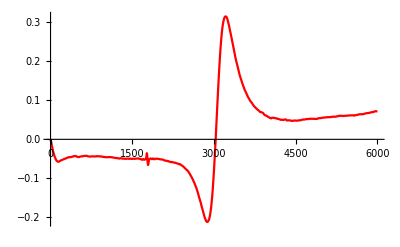

```mathematica
ClearAll[Int2];
Int21:=Integrate[data1Inter[x],x]
Int22:=Integrate[data2Inter[x],x]

gr1 = Plot[Evaluate[(Int22-Int21)/.x->x],{x,0,6000},PlotStyle->Red]
```

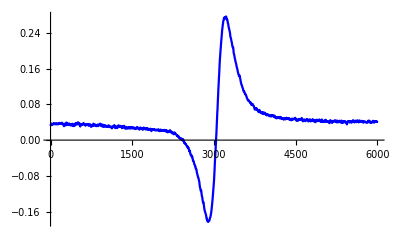

```mathematica
gr2=ListLinePlot[Transpose[{data1[[All,1]],data1[[All,2]]*30}],PlotRange->All,PlotStyle-> Blue]
```

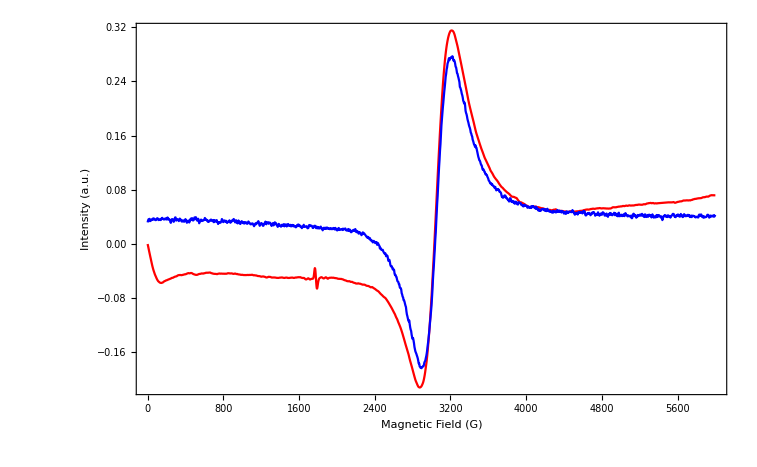

```mathematica
Show[gr1,gr2, Frame-> True, FrameLabel-> {"Magnetic Field (G)","Intensity (a.u.)"}]
```

```mathematica
Export["C:\\Users\\User\\Desktop\\1.png",%138,"PNG"]
```

C:\Users\User\Desktop\1.png